```mathematica
SetDirectory["~/Documents/GitHub/GriesSchneiderScripts/mathematica"]
```

/home/rebcabin/Documents/GitHub/GriesSchneiderScripts/mathematica

```mathematica
Block[{Print},<< "GS1.m"]
```

{total right,61,total wrong,0}

```mathematica
Block[{Print},<< "GS2.m"]
```

{total right,48,total wrong,0}

```mathematica
Block[{Print},<< "GS3.m"]
```

{total right,45,total wrong,0}

```mathematica
propositions
```

propositions

```mathematica
ClearAll[e,a,b,c,d];
```

```mathematica
propositions={
e[e[a,b],e[c,d]],
e[e[e[a,b],c],d],
e[e[a,e[b,c]],d],
e[a,e[e[b,c],d]],
e[a,e[b,e[c,d]]]};
```

```mathematica
ClearAll[e,f,l,n,p,r,t];
```

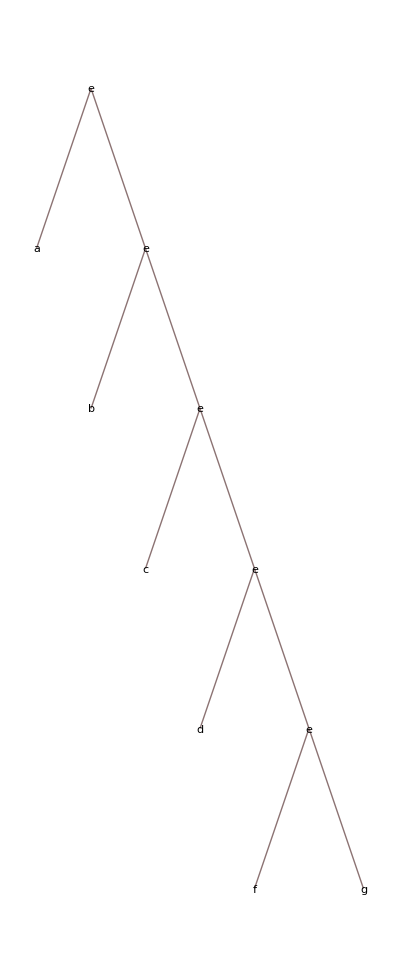
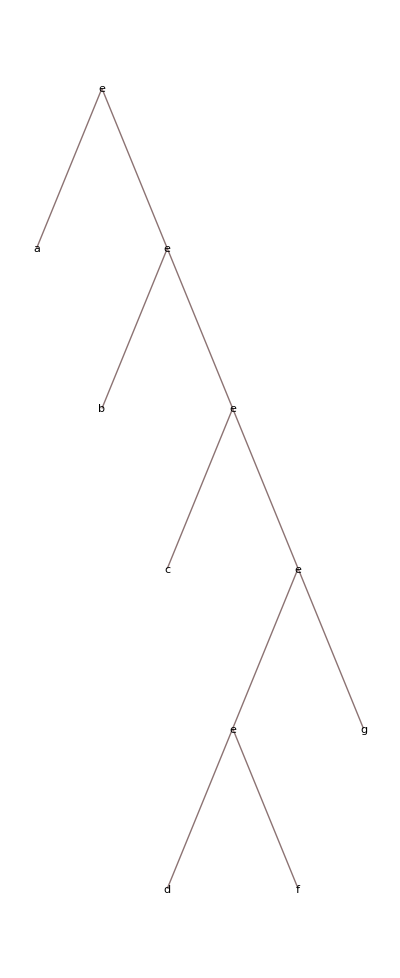
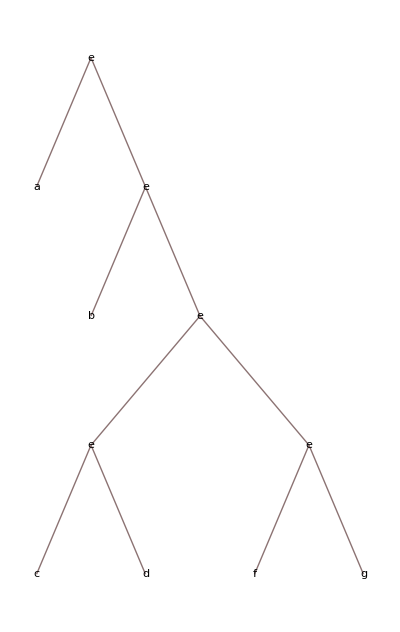
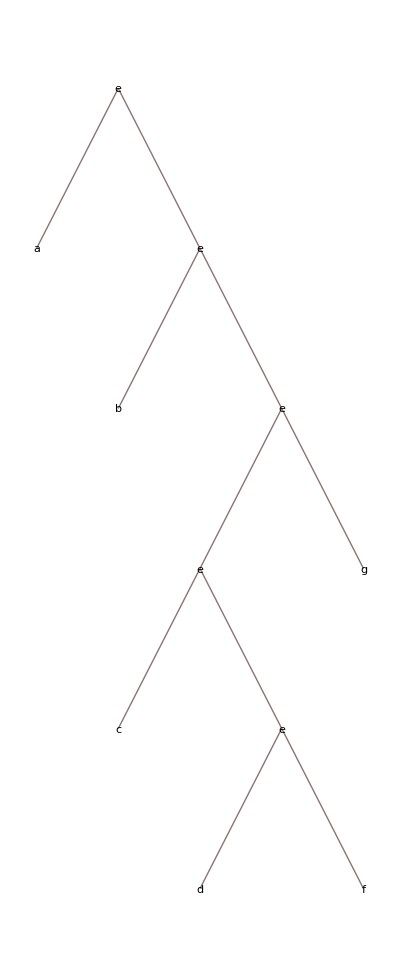
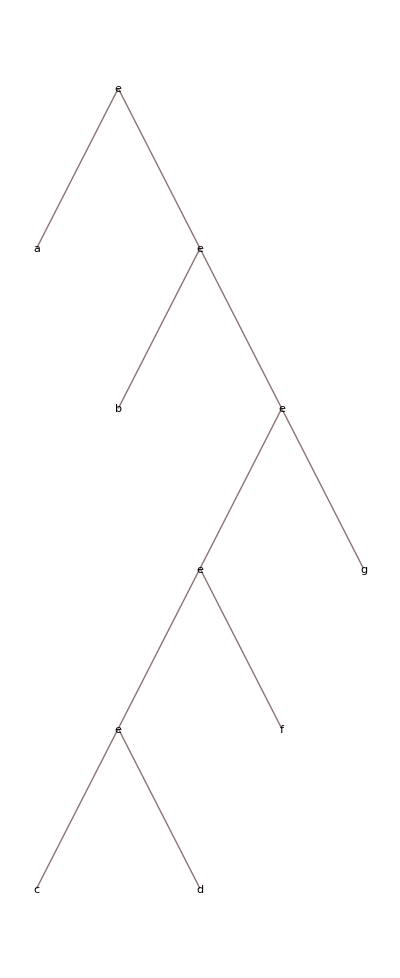
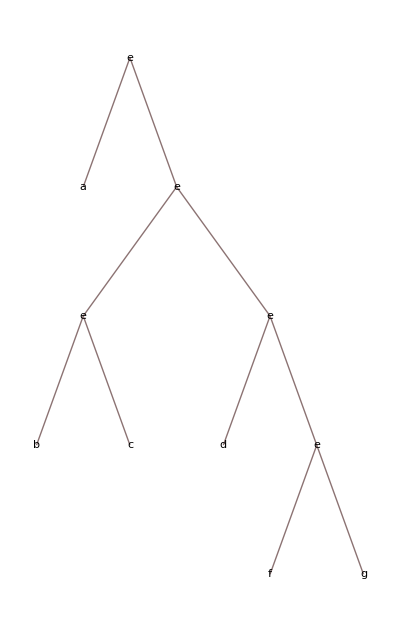
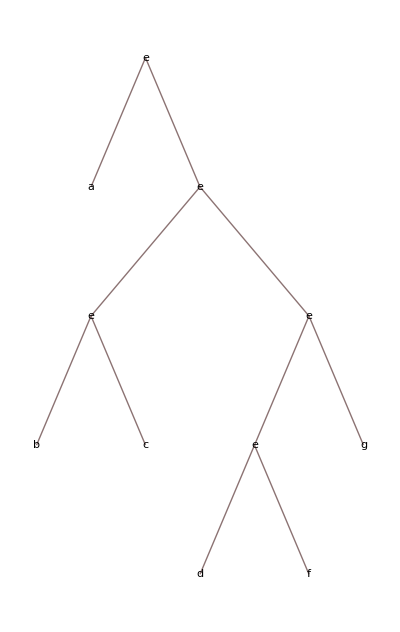
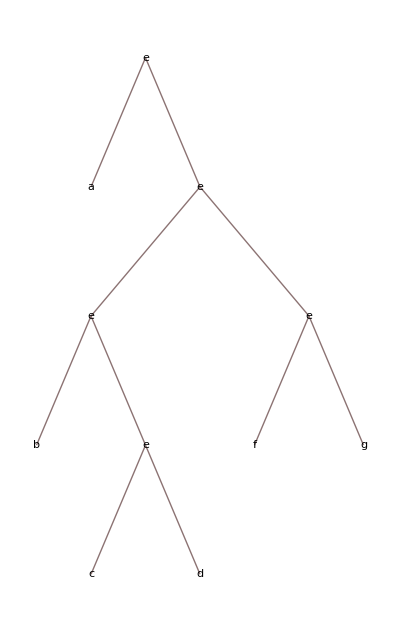

```mathematica
ClearAll[spl,dsc,lefts,rights,frights,flefts,cons,car,cdr];
cons[a_,h_[bs___]]:=h[a,bs];
car[h_[a_,___]]:=a;
cdr[h_[a_,bs___]]:=h[bs];
cadr[h_[a_,bs___]]:=car[cdr[h[a,bs]]];

spl[h_[a_,b_]]:={h[a,b]};
spl[h_[a_]]:={a};
spl[xs:h_[a_,bs__]]:=
Module[{L=Length[xs]-1,lefts,rights,flefts,frights,flr},
lefts=Table[xs⟦;;i⟧,{i,L}];
rights=Table[xs⟦i+1;;⟧,{i,L}];
flefts=spl/@lefts;
frights=spl/@rights;
Flatten[MapThread[Tuples@*h,{flefts,frights}],1]]
TreeForm/@spl[e[a,b,c,d,f,g]]
```

```mathematica
Sort[propositions]===spl[e[a,b,c,d]]
```

True

```mathematica
spl[h_[a_,b_]]:={h[a,b]};
spl[h_[a_]]:={a};
spl[xs:h_[a_,bs__]]:=
Module[{L=Length[xs]-1,ls,rs},
ls=Table[xs⟦;;i⟧,{i,L}];
rs=Table[xs⟦i+1;;⟧,{i,L}];
Print[<|"ls"->ls,"rs"->rs,"lfs"->spl/@ls,"rfs"->spl/@rs|>];
Flatten[MapThread[Tuples@*h,{spl/@ls,spl/@rs}],1]]
```

```mathematica
spl[eqv[a,b,c,d]]
```

{eqv[a,eqv[b,eqv[c,d]]],eqv[a,eqv[eqv[b,c],d]],eqv[eqv[a,b],eqv[c,d]],eqv[eqv[a,eqv[b,c]],d],eqv[eqv[eqv[a,b],c],d]}

```mathematica
l{e[a,e[b,e[c,d]]],e[a,e[e[b,c],d]],e[e[a,b],e[c,d]],e[e[a,e[b,c]],d],e[e[e[a,b],c],d]}
```